## Gardner and eKdV solitons

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state7.mx"];
```

```mathematica
(* PMMA *)
AL=-1.41*10^9*4;
BL=-7.02*10^9*4;
CL=-3.91*10^9*4;
DL=10^12;
FL=10^12;
GL=-2.2584896459158383*^11;
HL=10^12;
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/2/(1+ν);
Ε=4.92*10^9;
ν=0.34;
ρ=1160;
R=0.005;
```

```mathematica
a1=(q1^2+4 q4-4 q1 (2 alpha1+alpha2))/(6 q1^2);
a2=(q1^2+4 q4-4 q1 (2 alpha1+alpha2))/(6 q1^2);
a3=(3 q1 q3-8 q4 beta1+q1 (q1+4 alpha1+2 alpha2)beta1)/(9 q1^2 Ε);
```

```mathematica
q1=alpha1+alpha2+alpha3;
q2=3 cGGood[1]+2 cGGood[2]+3 cGGood[3]+6 cGGood[4]+cGGood[5]+6 cGGood[6]+2 cGGood[7];
q3=cGGood[1]+cGGood[3]+2 cGGood[4]+cGGood[5]+2 cGGood[6];
q4=alpha4+alpha5+alpha6+alpha7;
```

```mathematica
beta4mod/beta1
Sqrt[beta1^2/(R^2 beta4mod)]
```

1.1132×10^10

336.531

```mathematica
beta4mod=beta4+(beta1^2(1-2a2)-a3 Ε beta1)/3;
c=Sqrt[E/ρ];
v=-(A beta1 c)/(6Ε);
F=Sqrt[(A beta1)/(3 Ε R^2 q1)];
B=Sqrt[1-(3 A beta4mod)/(2beta1 Ε)];
uG[x_,t_]=A/(1+B Cosh[F(x-v t)]);
uG[A_,x_,t_]=A/(1+B Cosh[F(x-v t)]);
```

```mathematica
uG[-0.1,x,0]
```

-0.1/(1+1.15732 Cosh[384.419 (0.+x)])

```mathematica
uG[A,x,t]
```

A/(1+√(1+3.3939 A) Cosh[1215.64 √A (-0.0516851 A t+x)])

```mathematica
uG[A_,b_,x_,t_]=A/(1+√(1-b A) Cosh[1215.6391160381625 √-A (0.0516851082161288 A t+x)]);
```

```mathematica
Manipulate[Plot[{uG[-A,3.3,x,0],uG[-A,0,x,0]},{x,-0.01/Sqrt[A],0.01/Sqrt[A]},PlotRange->Full],{b,0,10,0.1},{A,1,10^10}]
```

```mathematica
uKdV[A_,x_,t_]=uG[x,t]-(R^2 a1 D[uG[x,t], x,x]+a2/c x D[uG[x,t], t]+a3 Derivative[1,0][uG][x,t]Derivative[-1,0][uG][x,t]);
```

```mathematica
uKdV[-1,x,0]
```

-1/(1+2.09616 Cosh[1215.64 (0.+x)])+(4029.36 x Sinh[1215.64 (0.+x)])/(1+2.09616 Cosh[1215.64 (0.+x)])^2-((33.6467+0. ⅈ) ArcTan[(0.542813+0. ⅈ) Sech[607.82 x] (-1. Sinh[607.82 x]+2.09616 Sinh[62.8304 (0.+9.67397 x)])] Sinh[1215.64 (0.+x)])/(1+2.09616 Cosh[1215.64 (0.+x)])^2-0.0000370253 ((3.09767×10^6 Cosh[1215.64 (0.+x)])/(1+2.09616 Cosh[1215.64 (0.+x)])^2-(1.29864×10^7 Sinh[1215.64 (0.+x)]^2)/(1+2.09616 Cosh[1215.64 (0.+x)])^3)

```mathematica
Manipulate[Plot[uKdV[A,x,0],{x,-0.01,0.01},PlotRange->Full],{A,-1,-0.01}]
```

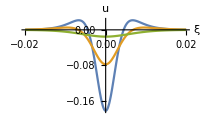

```mathematica
fig=Plot[{uKdV[-0.1,x,0],uKdV[-0.06,x,0],uKdV[-0.02,x,0]},{x,-0.02,0.02},PlotRange->Full,AxesLabel->{ξ,u},ImageSize->200]
```

```mathematica
Export["eKdV_solitons.pdf",fig]
```

eKdV_solitons.pdf